# Differences in the DiscreteWavelets and WaveletWare Packages

Accessing Multimedia Filespaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#236024063 | Modifications for the Haar Wavelet Transformationpaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#563135203
Continuous Scaling and Wavelet Functionspaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#32046898 | Replacement of and Improvements to Quantization Functionspaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#671537810
Wavelet Packet Transformspaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#19785884 | New Visualization Functions and Improved Graphicspaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#257561459
Consolidation of Wavelet Transform Routinespaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#389666502 | Improved Error Handlingpaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#9182496
Naming Convention for Inverse Wavelet Transformationspaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#453666235 | Other New Functions paclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#9186083
More Left- and Right-Wavelet Transformation Routinespaclet:WaveletWare/tutorial/Differences in the DiscreteWavelets and WaveletWare Packages#321236168 |

There are many new changes from the DiscreteWavelets package to the WaveletWare package.  Many of these changes are documented in this tutorial.  The reader is encouraged to view the help for particular functions as it is always more detailed than the information found in this tutorial.  


Two important notes to be considered before proceeding:

Mathematia 10.0 or above is required for the WaveletWare package.  This is because many WaveletWare functions make use of the Mathematica command AllTrue for error checking.

The documentation for the WaveletWare package has been completely overhauled and updated and can be fully integrated into Mathematica once the package is installed.

The table below lists the major differences between the DiscreteWavelets package and the WaveletWare package.

This loads the package:

```mathematica
<<WaveletWare`
```

## Accessing Multimedia Files

(top)

The DiscreteWavelets package has several routines that provide information and location of multimedia files that come with the package.  The WaveletWare consolidates these routines into three routines (one each for audio, data and images).  The chart below shows the new functions for accessing multimedia files.

WaveletWare | DiscreteWavelets
AudioInfo[opts] | AudioList, AudioNames
DataInfo[opts] | DataList, DataNames
ImageInfo[opts] | ImageList, ImageInfo

Routines for accessing multimedia files.

The tutorial Managing Image, Audio and Data Files in WaveletWare gives more detailed information on the uses of the functions in the above table.  Some simple calls are given below.

```mathematica
ImageInfo[]
ImageInfo[ImageForm->Color,DisplayInfo->True];
ImageInfo[ImageForm->Color,ShowThumbnails->True,ThumbnailSize->100,ThumbnailColumns->4];
```

{C:\ProgramData\Mathematica\Applications\WaveletWare\Images/benches.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/boys.jpg,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/bridge.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/building.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/canoes.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/car.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/chairs.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/chess.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/church.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/cups.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/dog.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/dome.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/facade.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/fingerprint.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/fish.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/goats.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/heads.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/landscape.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/legos.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/pigeon.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/road.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/tower.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/train.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/tram.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/waves.png,C:\ProgramData\Mathematica\Applications\WaveletWare\Images/yucca.png}

Information for Images in the WaveletWare Package
Image Number | Filename | Dimensions | Type | Max Iterations
1 | bridge.png | 512x768 | RGBColor | 8
2 | building.png | 768x512 | RGBColor | 8
3 | cups.png | 512x768 | RGBColor | 8
4 | facade.png | 512x768 | RGBColor | 8
5 | fish.png | 512x768 | RGBColor | 8
6 | goats.png | 512x768 | RGBColor | 8
7 | legos.png | 768x512 | RGBColor | 8
8 | waves.png | 768x512 | RGBColor | 8

-Graphics-

## Continuous Scaling and Wavelet Functions

(top)

The WaveletWare package contains routines that allow users to compute approximations of scaling, wavelet and packet functions.

PacketFunctionData[filter,n,opts] | Generate data to approximate a packet function
ScalingFunctionData[filter,opts] | Generate data to approximate a scaling function
WaveletFunctionData[filter,opts] | Generate data to approximate a wavelet function

Approximating scaling and wavelet functions.

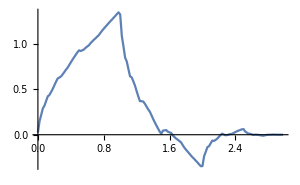

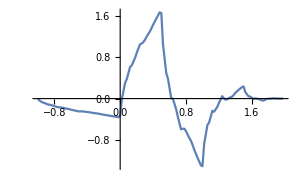

-Graphics-

```mathematica
data=ScalingFunctionData[Daub[4]];
ListPlot[data,Joined->True,ImageSize->300]

data=WaveletFunctionData[Daub[4]];
ListPlot[data,Joined->True,ImageSize->300]

data=Map[PacketFunctionData[Haar[],#]&,Range[0,3]];
Map[ListPlot[#,ImageSize->200]&,data] // GraphicsRow
```

## Wavelet Packet Transforms

(top)

The WaveletWare package contains many new functions that can be used to compute wavelet packet transformation and their inverses and visualize the results.  An entire tutorial is dedicated to these new functions (see Computing and Plotting Wavelet Packet Transforms) and the new packet functions are given in the List of Functions by Category Guide.  They are listed here as well for convenience.

BestBasisTree[data,opts] | Generate the best basis for a packet transform
FBIPacketTransform[data] | Wavelet packet transform for fingerprint compression
FBITree[] | Best basis tree for FBI packet transform
InverseFBIPacketTransform[{wt,t}] | Inverse FBI packet transform 
InverseWPT[{wt,t},filter,opts] | Inverse wavelet packet transform
NumberAboveThreshold[data,p] | Cost function for computing the best basis 
NumberNonzero[data] | Cost function for computing the best basis
ShannonEntropy[data] | Cost function for computing the best basis
SumOfPowers[data,p] | Cost function for computing the best basis
WPT[data,filter,opts] | Wavelet packet transform
WPTFull[data,filter,opts] | Full packet decomposition of data

Wavelet packet functions.

## Consolidation of Wavelet Transform Routines

(top)

One cumbersome feature of the DiscreteWavelets package was the many different routines associated with a single type of wavelet transformation.  

For example, computation of the Haar wavelet transform would require the use of HWT1D1, HWT1D, HWT2D1, or HWT2D based on the dimension of the data (vector or matrix) or the number of iterations to compute.  The Mathematica Map command was needed as well if the input was a list of three matrices from a color space.

In the WaveletWare package, all of these variants of the Haar wavelet transform have been replaced by the single routine HWTpaclet:WaveletWare/ref/HWT.  The HWTpaclet:WaveletWare/ref/HWT function takes as input a vector, matrix or list of three matrices each of the same dimension.  Moreover, the number of iterations can be stipulated as an option.

Below is a summary of the wavelet transform routines in the WaveletWare package and the routines they have replaced.

WaveletWare | DiscreteWavelets
HWT[data,opts] | HWT1D1, HWT1D, HWT2D1, HWT2D
WT[data,filter,opts] | WT1D1, WT1D, WT2D1, WT2D
BWT[data,filter,opts] | BWT1D1, BWT1D, BWT2D1, BWT2D
LWT[data,opts] | LWT1D1, LWT1D, LWT2D1, LWT2D

Wavelet transform routines in the WaveletWare package.

## Naming Convention for Inverse Wavelet Transformations

(top)

Inverse wavelet transformation routines in the DiscreteWavelets package started with the letter I and followed the convention described above so that several different names were needed to describe a single transformation.  In the WaveletWare package, inverse wavelet transform routines have been consolidated so that a single routine performs many tasks.  Moreover, inverse routines now start with the word "Inverse" rather than "I."  The chart below summarizes the changes:

WaveletWare | DiscreteWavelets
InverseHWT[data,opts] | IHWT1D1, IHWT1D, IHWT2D1
InverseWT[data,filter,opts] | IWT1D1, IWT1D, IWT2D1, IWT2DI
InverseBWT[data,filter,opts] | IBWT1D1, IBWT1D, IBWT2D1, IBWT2D
InverseLWT[data,opts] | ILWT1D1, ILWT1D, ILWT2D1, ILWT2D

Inverse wavelet transform routines in the WaveletWare package.

```mathematica
file=PackageDirectory[DataType->Images]<>"church.png";
A=ImageRead[file,Resize->{192,128}];
plt1=ImagePlot[A];
wt=HWT[A];
plt2=WaveletPlot[wt];

iwt=InverseHWT[wt];
plt3=ImagePlot[iwt];

GraphicsRow[{plt1,plt2,plt3},ImageSize->512]
```

-Graphics-

## More Left- and Right-Wavelet Transformation Routines

(top)

The DiscreteWavelets package contained the routines LeftHWT, RightHWT, LeftWT and RightWT.  These routines are for pedagogical use - in the case of the left-transform routines, the output is WApaclet:Global/ref/A where W is the associated matrix and Apaclet:Global/ref/A is an input matrix.  For the right-transform routines, the output is Apaclet:Global/ref/AW^T.  Inverse routines LeftIHWT, RightIHWT, LeftIWT and RightIWT were also provided.

The WaveletWare package contains these routines as well as left- and right-wavelet transform routines (and inverses) for the biorthogonal wavelet transform and the LeGall wavelet transform.  The inverse routines contain "Inverse" rather than "I."

LeftHWT[data,opts] | Left Haar wavelet transform
LeftWT[data,filter,opts] | Left wavelet transform
LeftBWT[data,filter,opts] | Left biorthogonal wavelet transform
LeftLWT[data,opts] | Left LeGall wavelet transform

Left wavelet transforms.

LeftInverseHWT[data,opts] | Left inverse Haar wavelet transform
LeftInverseWT[data,filter,opts] | Left inverse wavelet transform
LeftInverseBWT[data,filter,opts] | Left inverse biorthogonal wavelet transform
LeftInverseLWT[data,opts] | Left inverse LeGall wavelet transform

Left inverse wavelet transforms.

Replacing "Left" with "Right" in the two tables above give all the right-wavelet transform routines and their inverses.

```mathematica
file=PackageDirectory[DataType->Images]<>"chess.png";
A=ImageRead[file,Resize->{192,128}];
plt1=ImagePlot[A];

lwt=LeftLWT[A];
plt2=WaveletPlot[lwt,PlotType->Left];

rwt=RightLWT[A];
plt3=WaveletPlot[rwt,PlotType->Right];

GraphicsRow[{plt1,plt2,plt3},ImageSize->512]
```

-Graphics-

## Modifications for the Haar Wavelet Transformation

(top)

For pedagogical purposes, the discrete Haar wavelet transform is sometimes motivated using the filter (1/2, 1/2) rather than the orthogonal version ( (√2)/2, (√2)/2).  The WaveletWare version of the HWTpaclet:WaveletWare/ref/HWT routine reflects this approach and the cell below shows the matrix used (for data of length/dimension n) for the HWTpaclet:WaveletWare/ref/HWT computation.

```mathematica
n=8;
h={1/2,1/2};
WaveletMatrix[h,{n,n}] // MatrixForm
```

(1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2 | 1/2
-1/2 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 1/2)

The Orthogonalpaclet:WaveletWare/ref/Orthogonal option can be set to True and then the orthogonal filter ( (√2)/2, (√2)/2) is used for computation.  The cell below indicates the different outputs based on the value of the Orthogonalpaclet:WaveletWare/ref/Orthogonal option.

```mathematica
v=Range[10];
HWT[v,Computation->Symbolic]
HWT[v,Orthogonal->True,Computation->Symbolic] // Simplify
```

{3/2,7/2,11/2,15/2,19/2,1/2,1/2,1/2,1/2,1/2}

{3/(√2),7/(√2),11/(√2),15/(√2),19/(√2),1/(√2),1/(√2),1/(√2),1/(√2),1/(√2)}

## Replacement of and Improvements to Quantization Functions

(top)

The DiscreteWavelets package had functions nCEpaclet:WaveletWare/ref/nCE and Comppaclet:WaveletWare/ref/Comp that could be used to quantize data for image compression examples.  The functions are still part of the WaveletWare package.  They have been improved (for efficiency and accuracy) and also redundantly renamed in the WaveletWare package as PercentCEpaclet:WaveletWare/ref/PercentCE (nCEpaclet:WaveletWare/ref/nCE) and QuantizeCEpaclet:WaveletWare/ref/QuantizeCE (Comppaclet:WaveletWare/ref/Comp).   The cell below shows how these functions can be used.

```mathematica
file=PackageDirectory[DataType->Images]<>"road.png";
A=ImageRead[file,Resize->{128,192}];
ImagePlot[A]

wt=HWT[A,NumIterations->2];
WaveletPlot[wt,NumIterations->2]

ce=CE[wt];
k=PercentCE[ce,.995];
Print["The original image is comprised of ",Apply[Times,Dimensions[A]]," pixels.  The largest ",k," values represent 99.5% of the energy."];

Print["We convert the remaining ",Apply[Times,Dimensions[A]]-k," values to 0."];
newwt=QuantizeCE[wt,k];
WaveletPlot[newwt,NumIterations->2]

newA=InverseHWT[newwt,NumIterations->2];
ImagePlot[newA]
```

-Graphics-

-Graphics-

The original image is comprised of 24576 pixels.  The largest 4250 values represent 99.5% of the energy.

We convert the remaining 20326 values to 0.

-Graphics-

-Graphics-

## New Visualization Functions and Improved Graphics

(top)

The WaveletWare package includes vastly improved graphics capabilities compared to the DiscreteWavelets package.  Several improvements have been made to the plotting routines ImagePlotpaclet:WaveletWare/ref/ImagePlot, WaveletPlotpaclet:WaveletWare/ref/WaveletPlot (WaveletDensityPlot in the DiscreteWaveletsPackage) and WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot and new routines have been added.  Visualization routines for the WaveletWare package are listed below.

The "old" routines WaveletPlotpaclet:WaveletWare/ref/WaveletPlot and WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot along with the new routine WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot all contain an option argument tree.  If this argument is present, these routines will plot a wavelet packet transform (or parts of it, if desired).

ImagePlot[img,opts] | Plot an image
WaveletVectorPlot[v,opts] | Plot the wavelet transform of a vector
WaveletVectorPlot[v,tree,opts] | Plot the wavelet packet transform of a vector
WaveletPlot[data,opts] | Plot the wavelet transform of a matrix or 3 matrices
WaveletPlot[data,tree,opts] | Plot the wavelet packet transform of a matrix or 3 matrices
WaveletRegionPlot[data,iter,opts] | Plot a particular region(s) of a wavelet transform
WaveletRegionPlot[data,tree,iter,opts] | Plot a particular region(s) of a wavelet packet transform
FullWaveletPlot[data,opts] | Plot iterations of the (packet) transform of a matrix or matrices
FullWaveletVectorPlot[data,opts] | Plot iterations of the (packet) transform of a vector
ShowBestBasis[tree,opts] | Plot the best basis decomposition of a packet transform

Visualization routines in the WaveletWare package.

### ImagePlot

(top of section)

ImagePlotpaclet:WaveletWare/ref/ImagePlot can be used to plot grayscale or color images.  The input must be a matrix or list of three matrices each of the same dimensions.  The command below gives the options for ImagePlotpaclet:WaveletWare/ref/ImagePlot.  The first 5 are WaveletWare specific with the remainder being options for Mathematica's Raster and Image functions.  Of the first five, the Scalingpaclet:WaveletWare/ref/Scaling and PlotTogetherpaclet:WaveletWare/ref/PlotTogether options are new in WaveletWare.  

The Scalingpaclet:WaveletWare/ref/Scaling option uses the WaveletWare command MatrixStretchpaclet:WaveletWare/ref/MatrixStretch to apply a linear map that sends the min/max of each channel to prescribed values (the defaults are 0/255).  PlotTogetherpaclet:WaveletWare/ref/PlotTogether can be used for color images.  By default, a color image is plotted using all three color channels but setting PlotTogetherpaclet:WaveletWare/ref/PlotTogether to False instructs ImagePlotpaclet:WaveletWare/ref/ImagePlot to plot color channels separately.

```mathematica
Options[ImagePlot]
```

{ChannelColor→GrayLevel[1],Border→True,BorderColor→GrayLevel[0],Scaling→False,PlotTogether→True,AlignmentPoint→Center,BaselinePosition→Automatic,ColorSpace→Automatic,ImageResolution→Automatic,ImageSize→Automatic,Interleaving→Automatic,Magnification→Automatic,MetaInformation→{},TaggingRules→{},ColorFunction→Automatic,ColorFunctionScaling→True}

```mathematica
file=PackageDirectory[DataType->Images]<>"waves.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

ImagePlot[A,PlotTogether->False]
ImagePlot[A,PlotTogether->False,ChannelColor->{Red,Green,Blue}]
```

-Graphics-

-Graphics-

-Graphics-

### WaveletVectorPlot

(top of section)

The output of the cell below shows the options for WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot.  The options ImageSize, Background, Joined, PointSize and Ticks and Mathematica options for the ListPlot functions.  All other options are part of the WaveletWare package.  Of these WaveletWare options, Iterationpaclet:WaveletWare/ref/Iteration is explained in detail in the tutorial Data Structures in the WaveletWare Package and Dimmingpaclet:WaveletWare/ref/Dimming is a new option.  The Colorspaclet:WaveletWare/ref/Colors option is a consolidation of the options UseColors and ColorList for WaveletVectorPlot from the DiscreteWavelets package.

```mathematica
Options[WaveletVectorPlot]
```

{NumIterations→1,Iteration→All,DivideLines→True,DivideLinesColor→GrayLevel[0.5],Colors→{Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.6],Hue[0, 0.6, 0.6],Hue[0.08, 1, 0.8],Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55],Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55]},ImageSize→Automatic,Dimming→GrayLevel[0.8],Background→GrayLevel[1],Joined→False,PointSize→0.01,Ticks→Automatic}

In the case where particular iterations are specified to be plotted, the color value for Dimmingpaclet:WaveletWare/ref/Dimming indicates the color to use for regions not plotted.

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

wt=HWT[v,NumIterations->3];

WaveletVectorPlot[wt,NumIterations->3]
WaveletVectorPlot[wt,NumIterations->3,Colors->{Red,Green,Blue,Orange}]
WaveletVectorPlot[wt,NumIterations->3,Iteration->{{3,1},{3,2}}]
WaveletVectorPlot[wt,NumIterations->3,Iteration->{{3,1},{3,2}},Dimming->Lighter[Green]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot can also plot wavelet packet transforms - all that is needed is the optional second argument tree.

-Graphics-

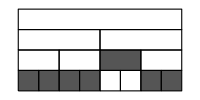

-Graphics-

-Graphics-

-Graphics-

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

{wt,tree}=WPT[v,Haar[],NumIterations->3,CostFunction->NumberAboveThreshold,SecondParameter->.1];
ShowBestBasis[tree,ImageSize->200]

WaveletVectorPlot[wt,tree,ImageSize->200]
WaveletVectorPlot[wt,tree,Iteration->{{3,1},{3,2},{3,7},{3,8}},ImageSize->200]
WaveletVectorPlot[wt,tree,Iteration->{{3,1},{3,2},{3,7},{3,8}},Dimming->Lighter[Purple],ImageSize->200]
```

### WaveletPlot

(top of section)

The output of the cell below displays all the options for the WaveletPlotpaclet:WaveletWare/ref/WaveletPlot function.  The first 12 options are from the WaveletWare package while the remaining options are for the Mathematica functions Raster and Image.

The Iterationpaclet:WaveletWare/ref/Iteration option consolidates the Region and Iteration option for WaveletDensityPlot in the DiscreteWavelets package and is described in detail in the tutorial Data Structures in the WaveletWare Package.  New options are PlotTogetherpaclet:WaveletWare/ref/PlotTogether, Scalingpaclet:WaveletWare/ref/Scaling, Dimmingpaclet:WaveletWare/ref/Dimming, DimmingRangepaclet:WaveletWare/ref/DimmingRange and PlotTypepaclet:WaveletWare/ref/PlotType.

```mathematica
Options[WaveletPlot]
```

{PlotType→Automatic,Iteration→All,NumIterations→1,PlotTogether→False,Scaling→True,ChannelColor→GrayLevel[1],Dimming→GrayLevel[0.8],DimmingRange→{200,255},DivideLines→True,DivideLinesColor→GrayLevel[1],Border→True,BorderColor→GrayLevel[0],AlignmentPoint→Center,BaselinePosition→Automatic,ColorSpace→Automatic,ImageResolution→Automatic,ImageSize→Automatic,Interleaving→Automatic,Magnification→Automatic,MetaInformation→{},TaggingRules→{},ColorFunction→Automatic,ColorFunctionScaling→True}

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{128,192}];
ImagePlot[A]

wt=HWT[A,NumIterations->3];
WaveletPlot[wt,NumIterations->3]
WaveletPlot[wt,NumIterations->3,Scaling->False]

WaveletPlot[wt,NumIterations->3,Iteration->{{3,2,2},{2,2,2},{1,2,2}}]
WaveletPlot[wt,NumIterations->3,Iteration->{{3,2,2},{2,2,2},{1,2,2}},Dimming->Yellow]
WaveletPlot[wt,NumIterations->3,Iteration->{{3,2,2},{2,2,2},{1,2,2}},Dimming->Yellow,DimmingRange->{0,255}]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

The PlotTypepaclet:WaveletWare/ref/PlotType option can be set to Left or Right if a left- or right-wavelet transform is to be plotted.

```mathematica
file=PackageDirectory[DataType->Images]<>"chairs.png";
A=ImageRead[file,Resize->{128,192}];
ImagePlot[A]

wt=LeftHWT[A];
WaveletPlot[wt,PlotType->Left]
```

-Graphics-

-Graphics-

WaveletPlotpaclet:WaveletWare/ref/WaveletPlot can also be used with color images.

```mathematica
file=PackageDirectory[DataType->Images]<>"bridge.png";
A=ImageRead[file,Resize->{128,192}];
ImagePlot[A]

wt=HWT[A,NumIterations->3];
WaveletPlot[wt,NumIterations->3]
WaveletPlot[wt,NumIterations->3,PlotTogether->True]

WaveletPlot[wt,NumIterations->3,Iteration->{{1,3,1,1},{2,2,1,2},{1,1,2,1}}]
WaveletPlot[wt,NumIterations->3,Iteration->{{All,3,1,1},{All,3,1,2}},PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

If WaveletPlotpaclet:WaveletWare/ref/WaveletPlot is provided with the option second argument tree, it can plot wavelet packet transformations.

```mathematica
file=PackageDirectory[DataType->Images]<>"car.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

{wt,tree}=WPT[A,Haar[],NumIterations->2,CostFunction->NumberAboveThreshold,SecondParameter->20];
ShowBestBasis[tree,Show3D->False]

WaveletPlot[wt,tree]
WaveletPlot[wt,tree,Iteration->{{1,1,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}]
WaveletPlot[wt,tree,Iteration->{{1,1,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}},Dimming->Lighter[Pink]]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

### WaveletRegionPlot

(top of section)

WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot is a new routine in the WaveletWare package.  There are redundancies between it and WaveletPlotpaclet:WaveletWare/ref/WaveletPlot and FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot, but the major difference is WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot produces individual plots of prescribed regions of a wavelet (packet) transformation.  The options for WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot are contained in the output of the cell below.  

Note that all options are part of the WaveletWare package except Background, Joined, PointSize, Ticks and ImageSize.  The last option, PresentationStylepaclet:WaveletWare/ref/PresentationStyle, allows the output to be formatted using either GraphicsColumn, GraphicsRow, or FlipView.

```mathematica
Options[WaveletRegionPlot]
```

{NumIterations→1,ChannelColor→GrayLevel[1],Border→True,BorderColor→GrayLevel[0],Scaling→True,PlotTogether→False,Colors→{Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.6],Hue[0, 0.6, 0.6],Hue[0.08, 1, 0.8],Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55],Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55]},Background→GrayLevel[1],Joined→False,PointSize→0.01,Ticks→Automatic,ImageSize→Automatic,PresentationStyle→{}}

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];
ListPlot[v,Ticks->{Range[0,n,n/4],Range[-1/2,1/2]},PlotLabel->"Data Samples"]

wt=HWT[v,NumIterations->3];
WaveletVectorPlot[wt,NumIterations->3]
WaveletRegionPlot[wt,{{3,1},{3,2}},NumIterations->3]
(* Click the mouse on the last plot to cycle through the graphs *)
WaveletRegionPlot[wt,{{3,1},{3,2}},NumIterations->3,PresentationStyle->FlipView]
```

-Graphics-

-Graphics-

-Graphics-

WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot can be used for images as well.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

wt=HWT[A,NumIterations->2];

WaveletPlot[wt,NumIterations->2,Iteration->{{2,1,1},{2,1,2},{2,2,1},{2,2,2}}]
WaveletRegionPlot[wt,{{2,1,1},{2,1,2},{2,2,1},{2,2,2}},NumIterations->2]
(* Click on the mouse to scroll through the different regions of the last plot *)
WaveletRegionPlot[wt,{{2,1,1},{2,1,2},{2,2,1},{2,2,2}},NumIterations->2,PresentationStyle->FlipView]
```

-Graphics-

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Adding the second optional argument tree allows WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot to plot portions of wavelet packet transformations.

```mathematica
file=PackageDirectory[DataType->Images]<>"benches.png";
A=ImageRead[file,Resize->{256,384}];
ImagePlot[A]

{wt,tree}=WPT[A,Haar[],NumIterations->2,CostFunction->NumberAboveThreshold,SecondParameter->20];
ShowBestBasis[tree,Show3D->False,ImageSize->300]

WaveletPlot[wt,tree]
WaveletRegionPlot[wt,tree,{{2,3,3},{2,3,4},{2,4,3},{2,4,4}}]
```

-Graphics-

-Graphics-

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### FullWaveletVectorPlot and FullWaveletPlot

(top of section)

FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot and FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot are two new visualization routines in the WaveletWare package.  They allow the user to plot several iterations of a wavelet transform or the full wavelet packet decomposition to a prescribed number of levels.

The options for FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot are contained in the output of the cell below.  The options Joined, PointSize, ImageSize and Ticks are Mathematica options for ListPlot.  Of the remaining WaveletWare options, most coincide with options for WaveletVectorPlotpaclet:WaveletWare/ref/WaveletVectorPlot with the exceptions being PacketPlotpaclet:WaveletWare/ref/PacketPlot (set to True if the input data is from a wavelet packet transform) and PresentationStylepaclet:WaveletWare/ref/PresentationStyle (see the WaveletRegionPlotpaclet:WaveletWare/ref/WaveletRegionPlot section above).

The input data for FullWaveletVectorPlotpaclet:WaveletWare/ref/FullWaveletVectorPlot must be generated from either WTFullpaclet:WaveletWare/ref/WTFull or WPTFullpaclet:WaveletWare/ref/WPTFull.

```mathematica
Options[FullWaveletVectorPlot]
```

{PacketPlot→False,Iteration→All,DivideLines→True,DivideLinesColor→GrayLevel[0.5],Colors→{Hue[0, 1, 0.72],Hue[0.06, 1, 0.9],Hue[0.17, 1, 0.4],Hue[0.11, 1, 0.72],Hue[0.06, 1, 0.72],Hue[0.12, 1, 0.9],Hue[0.5, 0.5, 0.5],Hue[0.17, 1, 0.6],Hue[0, 0.6, 0.6],Hue[0.08, 1, 0.8],Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55],Hue[0.11, 0.38, 0.64],Hue[0.08, 0.29, 0.5],Hue[0.08, 0.25, 0.64],Hue[0.08, 0.6, 0.6],Hue[0.11, 0.33, 0.72],Hue[0.11, 0.43, 0.5],Hue[0.13, 0.44, 0.72],Hue[0.08, 0.5, 0.6],Hue[0.06, 0.25, 0.7],Hue[0.11, 0.7, 0.55]},ImageSize→Automatic,Dimming→GrayLevel[0.8],Background→GrayLevel[1],Joined→False,PointSize→0.01,Ticks→Automatic,PresentationStyle→{}}

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];

wt=WTFull[v,Daub[4],NumIterations->4];
FullWaveletVectorPlot[wt]
(* Click on the mouse to scroll through the graphs in the last plot *)
FullWaveletVectorPlot[wt,PresentationStyle->FlipView]
```

-Graphics-

For wavelet packet plots, set PacketPlotpaclet:WaveletWare/ref/PacketPlot to True.

```mathematica
g[t_]:=Sqrt[t(1-t)]*Sin[2Pi (1.05)/(t+.05)];
n=1024;
v=g[Range[0,1-1/n,1/n]];

wt=WPTFull[v,Daub[4],NumIterations->4];
FullWaveletVectorPlot[wt,PacketPlot->True]
(* Click the mouse to scroll through the different graphs in the last plot *)
FullWaveletVectorPlot[wt,PacketPlot->True,PresentationStyle->FlipView]
```

-Graphics-

The options for FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot are shown in the output of the cell below.  The options PacketPlotpaclet:WaveletWare/ref/PacketPlot, Iterationpaclet:WaveletWare/ref/Iteration, PlotTogetherpaclet:WaveletWare/ref/PlotTogether, Scalingpaclet:WaveletWare/ref/Scaling, Dimmingpaclet:WaveletWare/ref/Dimming, DimmingRangepaclet:WaveletWare/ref/DimmingRange, DivideLinespaclet:WaveletWare/ref/DivideLines, DivideLinesColorpaclet:WaveletWare/ref/DivideLinesColor, Borderpaclet:WaveletWare/ref/Border, BorderColorpaclet:WaveletWare/ref/BorderColor, ChannelColorpaclet:WaveletWare/ref/ChannelColor and PresentationStylepaclet:WaveletWare/ref/PresentationStyle are all part of the WaveletWare package.  The remaining options are Mathematica options for the Image and Raster functions.

```mathematica
Options[FullWaveletPlot]
```

{PacketPlot→False,Iteration→All,PlotTogether→False,Scaling→True,Dimming→GrayLevel[0.8],DimmingRange→{200,255},DivideLines→True,DivideLinesColor→GrayLevel[1],Border→True,BorderColor→GrayLevel[0],ChannelColor→GrayLevel[1],PresentationStyle→{},ColorFunction→Automatic,ColorFunctionScaling→True,AlignmentPoint→Center,BaselinePosition→Automatic,ColorSpace→Automatic,ImageResolution→Automatic,ImageSize→Automatic,Interleaving→Automatic,Magnification→Automatic,MetaInformation→{},TaggingRules→{}}

The input data for FullWaveletPlotpaclet:WaveletWare/ref/FullWaveletPlot should be generated by WTFullpaclet:WaveletWare/ref/WTFull or WPTFullpaclet:WaveletWare/ref/WPTFull.

```mathematica
file=PackageDirectory[DataType->Images]<>"church.png";
A=ImageRead[file,Resize->{192,128}];

wt=WTFull[A,SplineFilters[2,2],NumIterations->3];
FullWaveletPlot[wt]

file=PackageDirectory[DataType->Images]<>"fish.png";
A=ImageRead[file,Resize->{128,192}];

wt=WTFull[A,Daub[4],NumIterations->3];
FullWaveletPlot[wt]
FullWaveletPlot[wt,PlotTogether->True]
```

-Graphics-

-Graphics-

-Graphics-

To plot wavelet packet transforms, set the PacketPlotpaclet:WaveletWare/ref/PacketPlot option to True.

```mathematica
file=PackageDirectory[DataType->Images]<>"chess.png";
A=ImageRead[file,Resize->{192,128}];

wt=WPTFull[A,SplineFilters[2,2],NumIterations->3];
FullWaveletPlot[wt,PacketPlot->True]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Improved Error Handling

(top)

While most will not use such routines, the WaveletWare package comes with more robust error handling than DiscreteWavelets.  The List of Functions by Category Guide lists all the error handling functions.  A couple of the more popular ones are listed below.  

CheckDatapaclet:WaveletWare/ref/CheckData returns a list of two numbers.  The first is the data type (1=vector, 2=matrix, 3=list of three matrices, 4=other) and the second is the max number of iterations of a wavelet transform that can be performed on the data.

CheckFilterpaclet:WaveletWare/ref/CheckFilter returns a 1 if the filter is (near) orthogonal, a 2 if it is a biorthogonal filter pair, or -1 otherwise.

```mathematica
v=Range[10];
A=ConstantArray[0,{10,10}];
B=ConstantArray[A,3];
c="Hello";

Map[CheckData,{v,A,B,c}]
```

{{1,1},{2,1},{3,1},{4,0}}

```mathematica
filters={Daub[4],SplineFilters[2,2],{1/2,1/2},{1,3,3,1}};
Map[CheckFilter,filters]
```

{1,2,1,-1}

## Other New Functions

(top)

Several new functions, not mentioned above, have been added to the WaveletWare package.  They are listed below.

AudioFormats[] | List of Mathematica audio formats
DataFormats[] | List of Mathematica data formats
ImageFormats[] | List of Mathematica image formats
RGBToHSI[data] | Convert from RGB to HSI color space
HSIToRGB[data] | Convert from HSI to RGB color space
PackageDirectory[opts] | File path for WaveletWare installation
WhiteNoise[n,sigma] | Generate white noise
WaveletMatrix[filter,{n,m}] | Create a wavelet matrix
WaveletTree[n,opts] | Wavelet tree basis decomposition for packet transform
WTFull[data,filter,opts] | Compute several different iterations of wavelet transform

Other new WaveletWare functions.